## Exercises: measures of association between two variables

#### 1. A newspaper asks two of its staff to review the coffee quality at different trendy cafés. The coffee can be rated on a scale from 1 (miserable) to 10 (excellent). The results of the two coffee enthusiasts X and Y are as follows: -Graphics- (a) Calculate and interpret Spearman’s rank correlation coefficient with pen and paper and then check your results using Mathematica. (b) Does Spearman’s R differ depending on whether ranks are assigned in a decreasing or increasing order? -> R does not differ: using a decreasing order for the ranks. The sum of d_i^2 =8, as before, and hence, the result for R is the same. (c) Suppose the coffee can only be rated as either good (>5) or bad (≤5). Do the chances of a good rating differ between the two journalists?

```mathematica
(*a*)
cafe = {{3,6},{8,7},{7,10},{9,8},{5,4}};
SpearmanRho = N[SpearmanRho[cafe[[All,1]],cafe[[All,2]]]]
```

0.6

```mathematica
(*c*)
oddsratio = N[(2*4)/(3*1)]
```

2.66667

#### 2. We are interested in the pizza delivery data previously discussed. (a) Read in the data and create two new binary variables which describe whether a pizza was hot (>65 ◦C) and the delivery time was short (<30 min). Create a contingency table for the two new variables. (b) Calculate and interpret the odds ratio for the contingency table from (a). (c) Use Cramer’s V and a stacked bar chart to explore the association between the categorical time and temperature variables. (d) Draw a scatter plot for the continuous time and temperature variables. Determine both the Bravais–Pearson and Spearman correlation coefficients. (e) Use methods of your choice to explore the relationship between temperature and driver, operator, number of ordered pizzas and bill. Is it clear which of the variables influence the pizza temperature?

```mathematica
(*a*)

pdt = Import["D:\\University_of_Aberdeen\\Semester_2\\PX5510_Statistics_and_Time_Series_Analysis\\Lecture Practicals\\pizza_delivery.csv"];
shortcold = Length[Select[pdt[[2;;]],#[[3]]<30&&#[[7]]<=65&]]
longcold =  Length[Select[pdt[[2;;]],#[[3]]>=30&&#[[7]]<=65&]]
shorthot = Length[Select[pdt[[2;;]],#[[3]]<=30&&#[[7]]>=65&]]
longhot = Length[Select[pdt[[2;;]],#[[3]]>= 30&&#[[7]]>=65&]]
conttable = {{"Cold temp.", shortcold, longcold, shortcold+longcold},
{"Hot temp.", shorthot, longhot, shorthot+longhot},
{"Sum", shortcold+shorthot,longcold+longhot,shortcold+shorthot+longcold+longhot}};
Join[{{"","Short time","long time", "sum"}},
conttable]//TableForm
```

101

691

213

261

| Short time | long time | sum
Cold temp. | 101 | 691 | 792
Hot temp. | 213 | 261 | 474
Sum | 314 | 952 | 1266

```mathematica
(*b*) OR = N[(shortcold*longhot)/(shorthot*longcold)]
```

0.179104

101 | 691 | 792
213 | 261 | 474
314 | 952 | 1266

{{46.3664,15.2931},{77.473,25.5531}}

164.686

0.360671

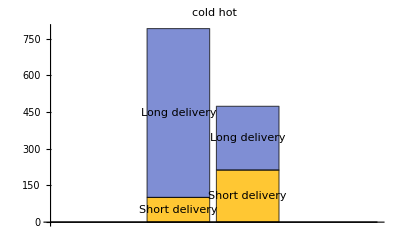

```mathematica
(*c*) conttable2 = {{shortcold, longcold, shortcold+longcold},
{shorthot, longhot, shorthot+longhot},
{shortcold+shorthot,longcold+longhot,shortcold+shorthot+longcold+longhot}};

conttable2//TableForm

n11 = N[(conttable2[[1,3]]*conttable2[[3,1]])/conttable2[[3,3]]];
n12 = N[(conttable2[[1,3]]*conttable2[[3,2]])/conttable2[[3,3]]];
n21 = N[(conttable2[[2,3]]*conttable2[[3,1]])/conttable2[[3,3]]];
n22 = N[(conttable2[[2,3]]*conttable2[[3,2]])/conttable2[[3,3]]];

expfreq = {{n11,n12},{n21,n22}};

chimatrix = Table[(conttable2[[i,j]]-expfreq[[i,j]])^2/expfreq[[i,j]],{i,1,2},{j,1,2}]
Total[chimatrix, 2]

cramerv = Sqrt[Total[chimatrix,2]/(conttable2[[3,3]]*(2-1))]

(*Creating a bar chart*)

BarChart[{conttable2[[1,1;;2]],conttable2[[2,1;;2]]},
ChartLabels->{"Short delivery","Long delivery"},
ChartLayout->"Stacked",PlotLabel->"cold        hot"]
```

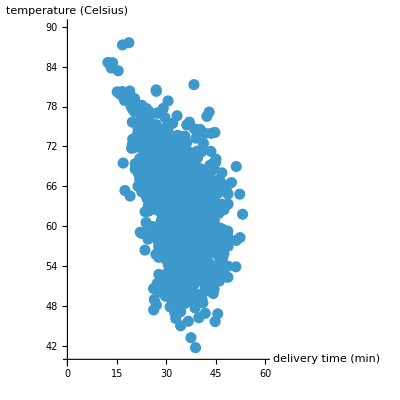

```mathematica
(*d*) 

deltime = pdt[[2;;,3]];
temp = pdt[[2;;,7]];
set = Transpose[{deltime, temp}];

ListPlot[set,
AxesLabel->{"delivery time (min)",
"temperature (Celsius)"},
PlotRange->{{0,60},{40,90}}, AspectRatio->1,
LabelStyle->{FontSize->14},PlotStyle->PointSize[0.02]]
```

```mathematica
Correlation[set[[;;,1]],set[[;;,2]]]
```

-0.433935

```mathematica
SpearmanRho[set[[;;,1]],set[[;;,2]]]
```

-0.39128